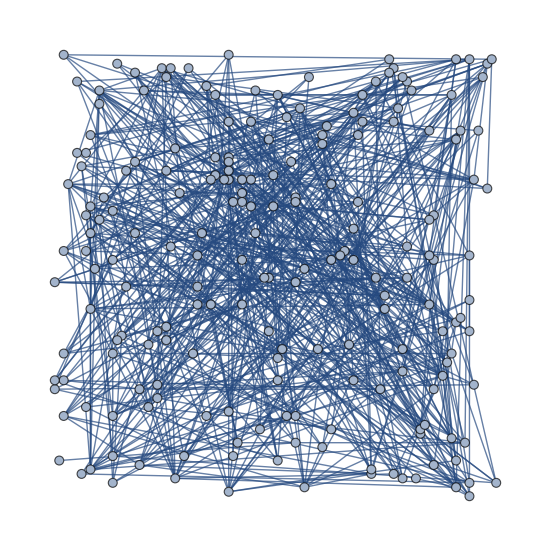

```mathematica
graph=Import[FileNameJoin[{NotebookDirectory[],"graph.dat"}]];

{n,e,r} = graph[[1]];
coords = graph[[2;;n+1]];
edges = graph[[n+2;;]];

Graph[First@#<->Last@#&/@edges,VertexCoordinates->coords, VertexSize->2]
Graph[First@#<->Last@#&/@edges,VertexSize->2];
```